```mathematica
Import["https://qtechtheory.org/questlink.m"]
CreateDownloadedQuESTEnv[];
(*Key Variables*)
numQs = 5;
deltaT = 0.15;
start=Mod[1.0,deltaT];
layers = 7;
TargetEnergyLevel = 1;
```

QuESTlink::notice: Bug alert! Prior to this version (v0.19), SimplifyPaulis[] contained a bug whereby multiplying X and Z operators (targeting the same qubit) produced a Y operator with an incorrect sign. This bug occurred only when multiplying Pauli strings together, and did not affect other algebraic forms (like summing or exponentiation), though did affect the downstream function CalcPauliExpressionMatrix[]. Please check any previous calculations which passed products of Pauli-strings to SimplifyPaulis[] and CalcPauliExpressionMatrix[]. We sincerely apologise for any arising issues! Silence this warning using Quiet[].

```mathematica
myθ[num_]:=Subscript[θ,num];
generateAnsatzCircuit[circuitN_,nblock_]:=Module[{ansatz,c,blocks,paramCount},ansatz={};
c=1;
ansatz=Join[ansatz,Table[Subscript[Rx,qb][myθ[c++]],{qb,0,circuitN-1}]];
ansatz=Join[ansatz,Table[Subscript[Rz,qb][myθ[c++]],{qb,0,circuitN-1}]];
ansatz=Join[ansatz,Table[Subscript[Ry,qb][myθ[c++]],{qb,0,circuitN-1}]];
For[blocks=1,blocks<=nblock,blocks++,ansatz=Join[ansatz,Flatten@Table[{R[myθ[c++],Subscript[Z,qb]  Subscript[Z,qb+1]]},{qb,0,circuitN-2}]];
ansatz=Join[ansatz,Table[Subscript[Rx,qb][myθ[c++]],{qb,0,circuitN-1}]];
ansatz=Join[ansatz,Table[Subscript[Ry,qb][myθ[c++]],{qb,0,circuitN-1}]];];
paramCount=c-1;
Return@{ansatz,paramCount};];
pauli[type_,site_]:=Subscript[type,site]

getListOf3LocalPaulis[numQs_]:=Join[Flatten[Table[{pauli[type,site]},{site,0,numQs-1},{type,{X,Y,Z}}],1],Flatten[Table[{pauli[type1,site1],pauli[type2,site2]},{site1,0,numQs-1},{site2,site1+1,numQs-1},{type1,{X,Y,Z}},{type2,{X,Y,Z}}],3],Flatten[Table[{pauli[type1,site1],pauli[type2,site2],pauli[type3,site3]},{site1,0,numQs-1},{site2,site1+1,numQs-1},{site3,site2+1,numQs-1},{type1,{X,Y,Z}},{type2,{X,Y,Z}},{type3,{X,Y,Z}}],5]];

localpaulis=getListOf3LocalPaulis[numQs];
nCONS=Length@localpaulis;
Print@Length@localpaulis

computeFvector[ψ_,ψs_,hψ_,hamil_,operatorPool_]:=Module[{term2s,term3,vec},Do[ApplyCircuit[ψ,operatorPool[[k]],ψs[[k]]];,{k,1,Length@operatorPool}];
ApplyPauliString[ψ,hamil,hψ];
term2s=CalcInnerProducts[ψ,ψs];
term3=CalcInnerProduct[ψ,hψ];
vec=Conjugate@CalcInnerProducts[hψ,ψs]-term2s*term3;
Return[Join[Re@vec,Im@vec]];];
computeJacobian[ψ_,ψs_,hψ_,dψ_,hamil_,operatorPool_,ansatz_,params_]:=Module[{term1,term2,term3,term3a,term3b,en},ApplyCircuitDerivs[InitZeroState[ψ],ansatz,params,dψ];
ApplyCircuit[InitZeroState@ψ,ansatz/. params];
ApplyPauliString[ψ,hamil,hψ];
Do[ApplyCircuit[hψ,operatorPool[[k]],ψs[[k]]];,{k,1,Length@operatorPool}];
term1a=Table[CalcInnerProducts[dψ[[k]],ψs],{k,1,Length@dψ}]    (* <dψ_k|Subscript[O,k] H ψ>*);
Do[ApplyCircuit[ψ,operatorPool[[k]],hψ];
ApplyPauliString[hψ,hamil,ψs[[k]]];,{k,1,Length@operatorPool}];
(* <ψ|Subscript[O,k] H|dψ_k>*)term1b=Table[Conjugate@CalcInnerProducts[dψ[[k]],ψs],{k,1,Length@dψ}];
term1=(term1a+term1b);
Do[ApplyCircuit[ψ,operatorPool[[k]],ψs[[k]]];,{k,1,Length@operatorPool}];
ApplyPauliString[ψ,hamil,hψ];
en=CalcInnerProduct[ψ,hψ];
(*2Re<ψ|H ψ>*)term2=Table[2  Re@CalcInnerProducts[dψ[[k]],ψs],{k,1,Length@dψ}]*en    (*2Re<dψ_k|Subscript[H,a] ψ>*);
term3a=CalcInnerProducts[ψ,ψs];
(*2Re<ψ|Subscript[H,a] ψ>*)term3b=2  Re[CalcInnerProducts[hψ,dψ]];
energyGradient=term3b;
(*2Re<dψ_k|H ψ>*);
term3=KroneckerProduct[term3b,term3a];
jacobian=Transpose[term1-term2-term3];
Return[Join[Re@jacobian,Im@jacobian]];];
```

375

```mathematica
(* Sample spin chain Hamiltonian*)
Hamil = 0.1 Subscript[X, 0] Subscript[X, 1]+0.1 Subscript[X, 0] Subscript[X, 2]+0.1 Subscript[X, 1] Subscript[X, 2]+0.1 Subscript[X, 0] Subscript[X, 3]+0.1 Subscript[X, 1] Subscript[X, 3]+0.1 Subscript[X, 2] Subscript[X, 3]+0.1 Subscript[X, 0] Subscript[X, 4]+0.1 Subscript[X, 1] Subscript[X, 4]+0.1 Subscript[X, 2] Subscript[X, 4]+0.1 Subscript[X, 3] Subscript[X, 4]+0.1 Subscript[Y, 0] Subscript[Y, 1]+0.1 Subscript[Y, 0] Subscript[Y, 2]+0.1 Subscript[Y, 1] Subscript[Y, 2]+0.1 Subscript[Y, 0] Subscript[Y, 3]+0.1 Subscript[Y, 1] Subscript[Y, 3]+0.1 Subscript[Y, 2] Subscript[Y, 3]+0.1 Subscript[Y, 0] Subscript[Y, 4]+0.1 Subscript[Y, 1] Subscript[Y, 4]+0.1 Subscript[Y, 2] Subscript[Y, 4]+0.1 Subscript[Y, 3] Subscript[Y, 4]-0.5 Subscript[Z, 0]+0.3 Subscript[Z, 1]+0.1 Subscript[Z, 0] Subscript[Z, 1]+0.1 Subscript[Z, 2]+0.1 Subscript[Z, 0] Subscript[Z, 2]+0.1 Subscript[Z, 1] Subscript[Z, 2]-0.7 Subscript[Z, 3]+0.1 Subscript[Z, 0] Subscript[Z, 3]+0.1 Subscript[Z, 1] Subscript[Z, 3]+0.1 Subscript[Z, 2] Subscript[Z, 3]+0.2 Subscript[Z, 4]+0.1 Subscript[Z, 0] Subscript[Z, 4]+0.1 Subscript[Z, 1] Subscript[Z, 4]+0.1 Subscript[Z, 2] Subscript[Z, 4]+0.1 Subscript[Z, 3] Subscript[Z, 4];

(*High Energy Physics Hamiltonian*)
Hamil = 0.05 Subscript[X, 0] Subscript[X, 1]+0.05 Subscript[X, 1] Subscript[X, 2]+0.05 Subscript[X, 2] Subscript[X, 3]+0.05 Subscript[X, 3] Subscript[X, 4]+0.05 Subscript[Y, 0] Subscript[Y, 1]+0.05 Subscript[Y, 1] Subscript[Y, 2]+0.05 Subscript[Y, 2] Subscript[Y, 3]+0.05 Subscript[Y, 3] Subscript[Y, 4]+0.45 Subscript[Z, 0]+0.05 Subscript[Z, 1]+1.5 Subscript[Z, 0] Subscript[Z, 1]+0.45 Subscript[Z, 2]+1. Subscript[Z, 0] Subscript[Z, 2]+1. Subscript[Z, 1] Subscript[Z, 2]+0.05 Subscript[Z, 3]+0.5 Subscript[Z, 0] Subscript[Z, 3]+0.5 Subscript[Z, 1] Subscript[Z, 3]+0.5 Subscript[Z, 2] Subscript[Z, 3]-0.05 Subscript[Z, 4];

hamilO[numQs_, t_]:=Module[{hamil},hamil=Sum[(1-t)*Subscript[X,k-1],{k,1,numQs}];
Return@hamil;];

timeHamil[Hamil_, t_]:=Module[{hamil},
hamil=hamilO[numQs, t];
hamil+=t*Hamil;
Return@hamil;];
```

```mathematica
{ansatz,numParams}=generateAnsatzCircuit[numQs,layers];
Print["number of parameters:", numParams];
ψ=CreateQureg[numQs];
hψ=CreateQureg[numQs];
dψ=CreateQuregs[numQs,numParams];
ψs=CreateQuregs[numQs,nCONS];

(*MORPHING PARAM*)
(*adjust initial parameters to change the target energy level*)
params=Table[Subscript[θ,k]->If[2*numQs+1<=k<= 3*numQs ,If[k==12||k==11,-π/2,-π/2],0],{k,1,numParams}];
(*params=Table[Subscript[θ,k]->If[2*numQs+1<=k<= 3*numQs ,π,0],{k,1,numParams}];*)
randomStep=Table[Subscript[θ,k]->RandomReal[{-π/500,π/500}],{k,1,numParams}];
params[[;;,2]]=params[[;;,2]]+randomStep[[;;,2]];


ψ=CreateQureg[numQs];
ApplyCircuit[InitZeroState@ψ,ansatz/. params];
params;
hamil = ExpandAll@Chop@timeHamil[Hamil, 0];
hamilmat=CalcPauliStringMatrix[hamil];
realEnergy=Sort[Eigenvalues@hamilmat];
eigenvec = Eigenvectors@hamilmat;

totalIter = 1;
ansatz/. params;
GetQuregMatrix[ψ];
ApplyPauliString[ψ,hamil,hψ];
energy=Chop@CalcInnerProduct[hψ,ψ] ;
Print["energy computed:", energy];
Print["actual E:", realEnergy] ;
finalHamil = ExpandAll@Chop@timeHamil[Hamil, 1.0];
Print["Final hamil:", finalHamil];
```

number of parameters:113

energy computed:-4.99939

actual E:{-5.,-3.,-3.,-3.,-3.,-3.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,3.,3.,3.,3.,3.,5.}

Final hamil:0.05 X_0 X_1+0.05 X_1 X_2+0.05 X_2 X_3+0.05 X_3 X_4+0.05 Y_0 Y_1+0.05 Y_1 Y_2+0.05 Y_2 Y_3+0.05 Y_3 Y_4+0.45 Z_0+0.05 Z_1+1.5 Z_0 Z_1+0.45 Z_2+1. Z_0 Z_2+1. Z_1 Z_2+0.05 Z_3+0.5 Z_0 Z_3+0.5 Z_1 Z_3+0.5 Z_2 Z_3-0.05 Z_4

Inverse::luc: Result for Inverse of badly conditioned matrix {{18.0007,2.32169,1.52759,0.769593,-0.00926138,1.68993×10^-7,0.000324157,0.0000157162,-0.0000212976,-1.65758×10^-6,«103»},«9»,«103»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{18.2014,2.80649,-1.33596,0.45804,0.000853304,0.000691271,-0.016519,0.00792793,-0.00594541,8.78893×10^-6,«103»},«9»,«103»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{18.1928,-0.961074,-2.6244,1.17338,0.00221981,0.0000930982,-0.0206059,0.00163929,0.00485702,3.18785×10^-6,«103»},«9»,«103»} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

$Aborted

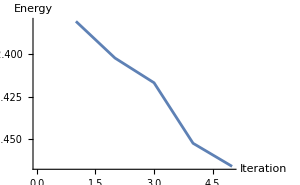
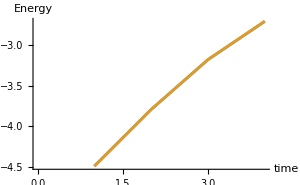

CalcPauliStringMatrix::error: Invalid arguments. See ?CalcPauliStringMatrix

actual e:Eigenvalues[$Failed]

CoVAR e:-2.46608

```mathematica
paramsList = {};
realEnergyList = {};
covarEnergy = {};
TargetEnergyList = {};
Monitor[
Do[
If[t==1.0,iter=50,iter=25];
hamil = ExpandAll@Chop@timeHamil[Hamil, t];
Monitor[
Do[(*Usually,you would sample from the operator pool,but for 5 qubits it is small enough that we can use all of it*)

operatorPool=RandomSample[localpaulis, nCONS];
vec=computeFvector[ψ,ψs,hψ,hamil, operatorPool];
jacobian=computeJacobian[ψ, ψs,hψ,dψ,hamil,operatorPool,ansatz,params];
vecDim = Dimensions[vec];
jacDim = Dimensions[jacobian];

(*
For shot noise simulation, add
vec = vec +RandomVariate[NormalDistribution[0, 1/10^3], vecDim];
jacobian = jacobian + RandomVariate[NormalDistribution[0, 1/10^3], jacDim];
*)
AppendTo[myVecNorms,Norm[vec]^2];
If[myVecNorms[[-1]] == myVecNorms[[-2]], Break[];];(*Calculate step from jacobian and F vector with regularisation*) 
Do[
eta=0.0001*2^etaIT;
jtj=Transpose[jacobian].jacobian;
stepvec=-0.5Inverse[jtj+eta*DiagonalMatrix@Diagonal@jtj].Transpose[jacobian].vec;
If[Max@Abs@stepvec>1,stepvec=stepvec/Max@Abs@stepvec];
paramsTST=params;
paramsTST[[;;,2]]=paramsTST[[;;,2]]+stepvec;
ApplyCircuit[InitZeroState@ψ,ansatz/.paramsTST];
newNORM=Norm[computeFvector[ψ,ψs,hψ,hamil, operatorPool]]^2;

If[newNORM<myVecNorms[[-1]],Break[];]
,{etaIT,0,10}];

(*Update parameters*)params[[;;,2]]=params[[;;,2]]+stepvec;
ansatz/. params;
ApplyCircuit[InitZeroState@ψ,ansatz/.params];
energy = CalcExpecPauliString[ψ, hamil, hψ];
 
count=count+1;

AppendTo[paramsList,params];
AppendTo[realEnergyList, energy];

,{step,1,iter}];
,Row[{ListLinePlot[realEnergyList, ImageSize->300, AxesLabel->{"Iteration","Energy"}]}]
];
realEnergyList = {};
(**)
realEnergy=Sort[Eigenvalues@CalcPauliStringMatrix[hamil]];
ansatz/. params;
ApplyCircuit[InitZeroState@ψ,ansatz/.params];
energy = CalcExpecPauliString[ψ, hamil, hψ];

AppendTo[covarEnergy,energy];
AppendTo[actualEnergyList, realEnergy];
AppendTo[TargetEnergyList, realEnergy[[TargetEnergyLevel]]];

totalIter = totalIter +1;,{t,start,1,deltaT}];,
Row[{ListLinePlot[{covarEnergy, TargetEnergyList}, ImageSize->300, AxesLabel->{"Time","Energy"}]}]
];
AppendTo[countList,count];
Row[{ListLinePlot[realEnergyList, ImageSize->300, AxesLabel->{"Iteration","Energy"}],ListLinePlot[{covarEnergy, TargetEnergyList}, ImageSize->300, AxesLabel->{"time","Energy"}]}]
(*Final comparison*)
hamil = ExpandAll@Chop@Hamil[1.0,0.1, 0,0.1,5,1.0];
hamilmat=CalcPauliStringMatrix[hamil];
realEnergy=Sort[Eigenvalues@hamilmat];
Print["actual e:", realEnergy];
Print["CoVAR e:", energy];
```